```mathematica
SetDirectory["/home/uyras/projects/partsEngine/build-PartsEngine-Desktop_Qt_5_4_0_GCC_64bit-Debug"];
```

```mathematica
(*Сохраняет в TIFF формате график посещенных энергий для каждого потока*)
energies = Union[ReadList["energies.txt"]];
ParallelTable[
Export["oe_"<>ToString[i]<>".tif",
data=ReadList["e_"<>ToString[i]<>".txt"];
dataLen=Length[data];
plot=Join[{data},Table[{{0,i},{dataLen,i}},{i,energies}]];
ListLinePlot[plot]
,"TIFF",ImageSize->1920
];,{i,0,49}
];
```

$Aborted

1.00098

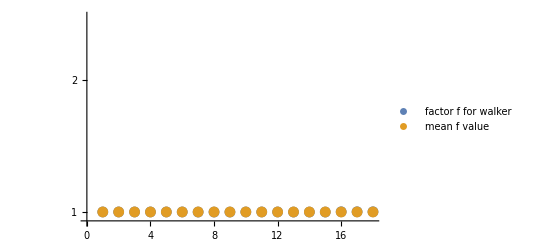

0 | 1.00098
1 | 1.00098
2 | 1.00098
3 | 1.00098
4 | 1.00098
5 | 1.00098
6 | 1.00049
7 | 1.00049
8 | 1.00049
9 | 1.00098
10 | 1.00098
11 | 1.00098
12 | 1.00049
13 | 1.00049
14 | 1.00049
15 | 1.00196
16 | 1.00196
17 | 1.00196

```mathematica
(* Выборка всех модификационных факторов из аналитики процесса*)
desc = OpenRead["analys.txt"];
Skip[desc,String];
data=Last/@ReadList[desc,Number,RecordLists->True];
mean = Mean[data](*Средний модификационный фактор*)
ListLogPlot[{data,Table[mean,{i,Length[data]}]},PlotRange->{0.95,2.8},PlotLegends->{"factor f for walker","mean f value"}]
Grid[Table[{i-1,data[[i]]},{i,1,Length[data]}],Frame->All]
```